```mathematica
<<"/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Clear[Ad,Bd,Ae,Be,qa,qb,td,tu,te,n,na,nrB,Zb,Z,Za]
ϵ=10^-5;
sysWExpCIsource=DynamicalSystem[{
Ae/te-Ad/(qa td),
Be/te-Bd/(qb td),
- Ae/te+(Ad/(td qa)+(1-Ad-Ae-Bd-Be)/tu)  (n (na)+(1-n)Ad/(Ad+Bd)),
- Be/te+(Bd/(td qb)+(1-Ad-Ae-Bd-Be)/tu)  (n (1-na)+(1-n)Bd/(Ad+Bd))
},
{{Ad,-0.01,1+0.01},{Bd,-0.01,1+0.01},{Ae,-0.01,1+0.01},{Be,-0.01,1+0.01}},
{{tu,ϵ,5000},{te,0.01,5000},{td,1,5000},{qa,ϵ,1},{qb,ϵ,1},{n,0,1},{na,0,1}}]
```

DynamicalSystem[«4 ODEs»,{Ad,Bd,Ae,Be},{tu,te,td,qa,qb,n,na}]

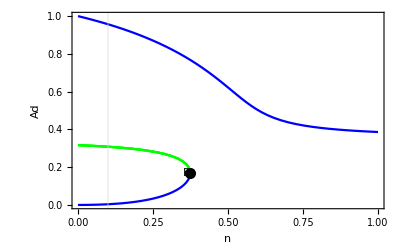

```mathematica
DisplayBifurcationDiagram[sysWExpCIsource/.{tu->1000,te->0.001,td->1300,qa->1,qb->0.82,na->0.5},n,StateVariables->{Ad},GridLines->{{0.1},{}}]
```

```mathematica
ER = EquilibriumBranches[sysWExpCIsource/.{tu->1000,te->0.001,td->1300,qa->1,qb->1,na->0.5},n];
```

```mathematica
ER[[1]][[5]][[4]]
```

{{0.999999230769823,-1.51049260897069×10^-16,7.69230177515248×10^-7,-1.16191739151592×10^-22,0},{0.991003051752352,0.000133936708316542,7.62310039809502×10^-7,1.03028237166571×10^-10,0.0227197087003612},{0.979898539066818,0.000652336977282981,7.53768106974475×10^-7,5.01797674833063×10^-10,0.0490398072904141},{0.968133186395253,0.00159914595443622,7.44717835688656×10^-7,1.23011227264325×10^-9,0.0750591570110866},{0.955678146634273,0.0030169175706708,7.35137035872518×10^-7,2.32070582359293×10^-9,0.100733822321637},{0.942507570647587,0.0049500470715015,7.25005823575067×10^-7,3.80772851653961×10^-9,0.126014753260273},{0.928599898482665,0.00744408197521348,7.14307614217434×10^-7,5.72621690401037×10^-9,0.150847855673468},{0.913939279341889,0.0105447976861243,7.03030214878376×10^-7,8.11138283548026×10^-9,0.175174350264784},{0.898517039976773,0.0142970392279714,6.91166953828287×10^-7,1.09977224830549×10^-8,0.198931491233108},{0.882333083685959,0.0187433615656727,6.78717756681507×10^-7,1.44179704351328×10^-8,0.222053695000447},{0.865397070685637,0.0239225393069284,6.65690054373567×10^-7,1.84019533130218×10^-8,0.244474090005653},{0.847729216289435,0.0298680559224612,6.52099397145719×10^-7,2.29754276326624×10^-8,0.266126440543668},{0.829360556920447,0.0366067132038469,6.37969659169575×10^-7,2.81590101568053×10^-8,0.286947328652539},{0.810332581505281,0.0441575124716803,6.23332755004062×10^-7,3.39673172859079×10^-8,0.306878412733158},{0.790696203869359,0.052530941876746,6.08227849130276×10^-7,4.04084168282662×10^-8,0.325868538692452},{0.770510145770334,0.0617287580080039,5.92700112131026×10^-7,4.74836600061569×10^-8,0.343875475340597},{0.749838887649049,0.0717442832692992,5.76799144345423×10^-7,5.51879102071532×10^-8,0.360867087154533},{0.728750402434396,0.0825631688657869,5.60577232641843×10^-7,6.35101298967591×10^-8,0.376821836805135},{0.70731390292257,0.0941645143046472,5.44087617632746×10^-7,7.24342417728055×10^-8,0.391728607189749},{0.685597805260388,0.106522200848305,5.27382927123376×10^-7,8.19401544986962×10^-8,0.405585923532647},{0.663668052324717,0.119606292277634,5.10513886403628×10^-7,9.20048402135647×10^-8,0.41840072038087},{0.641586869975757,0.133384376795683,4.93528361519813×10^-7,1.0260336676591×10^-7,0.43018682676497},{0.619411963729684,0.147822758867369,4.76470741330526×10^-7,1.13709814513361×10^-7,0.440963337644735},{0.597196114575161,0.162887448464954,4.59381626596278×10^-7,1.25298037280734×10^-7,0.450753010993921},{0.574987104211964,0.178544929390717,4.42297772470742×10^-7,1.37342253377475×10^-7,0.459580789896826},{0.552827889888606,0.194762713757056,4.25252222991235×10^-7,1.49817472120812×10^-7,0.46747250843148},{0.53075695223124,0.211509705432922,4.08274578639416×10^-7,1.6269977340994×10^-7,0.474453805685211},{0.50880875041984,0.228756402626421,3.913913464768×10^-7,1.75966463558786×10^-7,0.480549246913997},{0.48701423315456,0.246474971016277,3.74626333195815×10^-7,1.89596131550982×10^-7,0.485781634705358},{0.465401367918748,0.2646392162591,3.5800105224519×10^-7,2.03568627891615×10^-7,0.490171484551194},{0.44399566333682,0.283224480150139,3.41535125643708×10^-7,2.17864984730876×10^-7,0.493736636450261},{0.422820669241496,0.302207479507647,3.25246668647304×10^-7,2.32467291928959×10^-7,0.496491975098708},{0.401898446354954,0.3215661017822,3.09152651042273×10^-7,2.47358539832461×10^-7,0.498449234337755},{0.381250002536043,0.341279166877113,2.93269232720033×10^-7,2.62522436059318×10^-7,0.499616865714829},{0.360895695752927,0.361326160869609,2.77612073656097×10^-7,2.7794320066893×10^-7,0.499999955593803},{0.340855605702194,0.381686944271222,2.62196619770918×10^-7,2.93605341747094×10^-7,0.499600179853041},{0.321149876636763,0.402341435128507,2.47038366643664×10^-7,3.09493411637313×10^-7,0.498415789698603},{0.301799033719683,0.423269265608115,2.32153102861295×10^-7,3.25591742775473×10^-7,0.496441626476602},{0.282824274231488,0.44444940973579,2.17557134024222×10^-7,3.41884161335223×10^-7,0.493669167692815},{0.264247733287395,0.465859779730721,2.0326748714415×10^-7,3.5835367671594×10^-7,0.490086610806404},{0.246092721368465,0.487476789039058,1.89302093360358×10^-7,3.7498214541466×10^-7,0.485679005856026},{0.228383927903975,0.509274881959183,1.75679944541519×10^-7,3.91749909199371×10^-7,0.48042845258143},{0.211147581329906,0.53122603299348,1.6242121640762×10^-7,4.08635409994985×10^-7,0.474314382279264},{0.19441155151903,0.553299224152645,1.49547347322331×10^-7,4.25614787809727×10^-7,0.467313948804667},{0.178205375400882,0.575459915780247,1.37081058000679×10^-7,4.42661473677113×10^-7,0.459402556207552},{0.162560181386518,0.597669536336517,1.25046293374244×10^-7,4.59745797181936×10^-7,0.450554551369669},{0.147508483689866,0.619885028920115,1.1346806437682×10^-7,4.76834637630857×10^-7,0.440744107122411},{0.133083815112009,0.642058506393403,1.02372165470776×10^-7,4.93891158764156×10^-7,0.429946312728537},{0.119320168203037,0.664137081035291,9.1784744771567×10^-8,5.10874677719454×10^-7,0.418138472275702},{0.106251222233374,0.686062945497461,8.17317094102876×10^-8,5.27740727305739×10^-7,0.40530158599279},{0.0939093493330586,0.707773784830943,7.22379610254297×10^-8,5.44441372946879×10^-7,0.391421954896825},{0.0823244187732004,0.729203588904467,6.33264759793849×10^-8,5.60925837618821×10^-7,0.37649280850778},{0.0715224527195764,0.750283905661017,5.50172713227511×10^-8,5.7714146589309×10^-7,0.360515815504346},{0.0615242254819296,0.770945526419811,4.7326327293792×10^-8,5.93035020322931×10^-7,0.343502308801256},{0.0523439330557302,0.791120528740048,4.02645638890232×10^-8,6.0855425287696×10^-7,0.325474052009213},{0.0439880797975601,0.810744531608,3.38369844596616×10^-8,6.23649639698462×10^-7,0.306463403456928},{0.0364547243922982,0.829758959440247,2.80420956863832×10^-8,6.38276122646344×10^-7,0.286512798925679},{0.0297331931860808,0.84811308423112,2.2871687066216×10^-8,6.52394680177785×10^-7,0.265673565446088},{0.0238043095921531,0.865765631326727,1.83110073785793×10^-8,6.6597356255902×10^-7,0.244004175722814},{0.018641116570761,0.882685793375411,1.43393204390469×10^-8,6.78989071827239×10^-7,0.221568131403858},{0.0142100027258933,0.898853584839132,1.09307713276103×10^-8,6.9142583449164×10^-7,0.19843170385137},{0.0104720969958514,0.914259563346148,8.05545922757799×10^-9,7.03276587189345×10^-7,0.174661756068365},{0.00738478038243954,0.928904021698201,5.68060029418426×10^-9,7.14541555152462×10^-7,0.15032382587051},{0.00490317448251972,0.942795801145334,3.77167267886132×10^-9,7.25227539342565×10^-7,0.125480584806555},{0.00298149746933599,0.955950889443298,2.29345959179691×10^-9,7.35346838033306×10^-7,0.10019071845772},{0.00157421758866055,0.968390952392149,1.21093660666196×10^-9,7.4491611722473×10^-7,0.0745082160917467},{0.000636972453544779,0.980141915904509,4.89978810419061×10^-10,7.53955319926545×10^-7,0.0484820185458114},{0.00014434688389503,0.99065628841023,1.11036064534638×10^-10,7.620432987771×10^-7,0.0235694943403526},{0.0000309272138609372,0.995699650189117,2.37901645084132×10^-11,7.65922807837783×10^-7,0.0110232287285128},{5.63443391113673×10^-6,0.998169349619348,4.33417993164364×10^-12,7.67822576630268×10^-7,0.00472924503661425},{6.23505502030876×10^-7,0.999391389790843,4.79619616946827×10^-13,7.68762607531418×10^-7,0.00157723549689213},{0,0.999999,0,7.6923×10^-7,0},{-7.15178318747396×10^-19,0.999999230769823,-5.50137168267228×10^-25,7.69230177515248×10^-7,0}}

```mathematica
combinedCIn = {}
```

{}

```mathematica
For[i=1,i<=5,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

```mathematica
theFile=File["/Users/raina/Documents/ant22exten/newbif_t1/fig6/tu1000_te3000_td1300_qa1.0_qbvary_n0.05_na0.30.txt"]
```

File[/Users/raina/Documents/ant22exten/newbif_t1/fig6/tu1000_te3000_td1300_qa1.0_qbvary_n0.05_na0.30.txt]

```mathematica
Export[theFile,combinedCIn,"Table"];
```

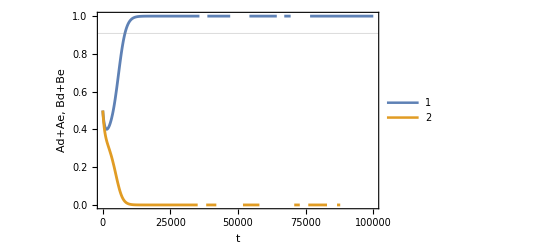

```mathematica
Clear[Ad,Bd,Ae,Be,qa,qb,td,tu,te,n,na,nrB,Zb,Z,Za];
qa = 1;
qb = 0.82;
td =1300;
te =0.01;
n=0;
na=0.5;
ep = 0.0001;
tu =1000;
tmax=100000;
outp4333441 =NDSolve[{
Ae'[t]==- Ae[t]/te+(Ad[t]/(td qa)+(1-Ad[t]-Ae[t]-Bd[t]-Be[t])/tu)  (n (na)+(1-n)Ad[t]/(Ad[t]+Bd[t])),
Be'[t]==- Be[t]/te+(Bd[t]/(td qb)+(1-Ad[t]-Ae[t]-Bd[t]-Be[t])/tu)  (n (1-na)+(1-n)Bd[t]/(Ad[t]+Bd[t])),
Ad'[t]==Ae[t]/te-Ad[t]/(qa td),
Bd'[t]==Be[t]/te-Bd[t]/(qb td)
,Bd[0]==0.5+ep,Ae[0]==0.0,Ad[0]==0.5-ep,Be[0]==0.0},{Ad,Bd,Ae,Be},{t,0,tmax}];
Plot[Evaluate[{Ad[t]+Ae[t], Bd[t]+ Be[t]} /. outp4333441], {t, 0,tmax}, PlotRange -> {{0,tmax},{0,1}}, PlotLegends -> Automatic,GridLines->{{}, {0.909}},Frame->True,FrameLabel->{"t","Ad+Ae, Bd+Be"},PlotStyle->Thickness[0.005]]
```